## Energy Function - B

```mathematica
ClearAll["Global`*"]
```

```mathematica
figPath="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
export[object_,name_]:=Export[StringTemplate["``/``.pdf"][figPath,name],object,ImageResolution->1200];
```

```mathematica
Hprime[x3_,phi3_,I_,u_,v0_]:=x3^2(u-Sin[phi3]^2-v0/I Cos[phi3])+I^2*Sin[phi3]^2+2v0*I*Cos[phi3];
```

```mathematica
IConst=19/2;
A1Const=1/(2*10);
A2Const=1/(2*20);
A3Const=1/(2*40);
thetaConst=70*π/180;
jConst=11/2;
```

```mathematica
u[A1_,A3_,A_]:=(A3-A1)/A;
A[I_,j_,theta_,A1_,A2_]:=A2(1-j*Sin[theta]/I)-A1;
v0[j_,theta_,A1_,A_]:=(-A1*j*Cos[theta])/A;
```

```mathematica
AConst[I_]:=A[I,jConst,thetaConst,A1Const,A2Const];
uConst[I_]:=u[A1Const,A3Const,AConst[I]];
v0Const[I_]:=v0[jConst,thetaConst,A1Const,AConst[I]];
```

```mathematica
opts={Frame->True,Axes->False,AspectRatio->0.85,ImageSize->420,FrameStyle->Directive[Black,Thick],LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"}};
```

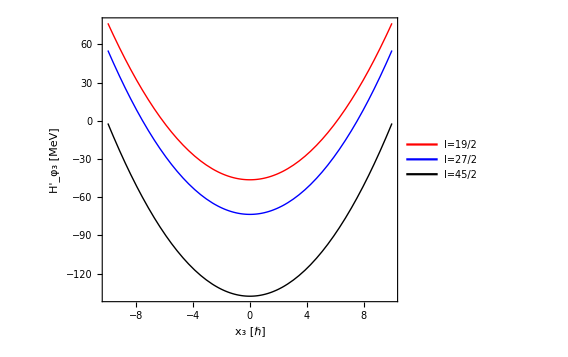

```mathematica
p1=Plot[{Hprime[x,π,19/2,uConst[19/2],v0Const[19/2]],Hprime[x,π,27/2,uConst[27/2],v0Const[27/2]],Hprime[x,π,45/2,uConst[45/2],v0Const[45/2]]},{x,-10,10},Evaluate[opts],FrameLabel->{"x_3 [ℏ]","H'_φ_3 [MeV]"},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick}},PlotLegends->Placed[{"I=19/2","I=27/2","I=45/2"},{0.38,0.78}]];
Show[p1]
export[p1,"Energy-Function-New-Boson-B1-phi3-const"];
```

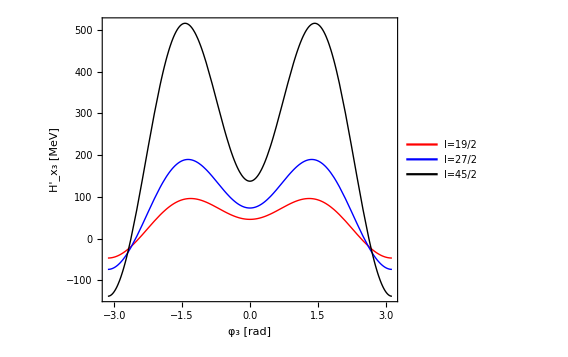

```mathematica
p2=Plot[{Hprime[0,x,19/2,uConst[19/2],v0Const[19/2]],Hprime[0,x,27/2,uConst[27/2],v0Const[27/2]],Hprime[0,x,45/2,uConst[45/2],v0Const[45/2]]},{x,-π,π},Evaluate[opts],FrameLabel->{"φ_3 [rad]","H'_x_3 [MeV]"},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick}},PlotLegends->Placed[{"I=19/2","I=27/2","I=45/2"},{0.67,0.16}]];
Show[p2]
export[p2,"Energy-Function-New-Boson-B1-x3-const"];
```